#### Functions

```mathematica
ClearAll["Global`*"];

(* import functions *)
Get["/Users/csfloyd/Dropbox/Projects/CoupledLearningMarkov/Mathematica/CLFunctions.m"];
```

#### Training graphs

15

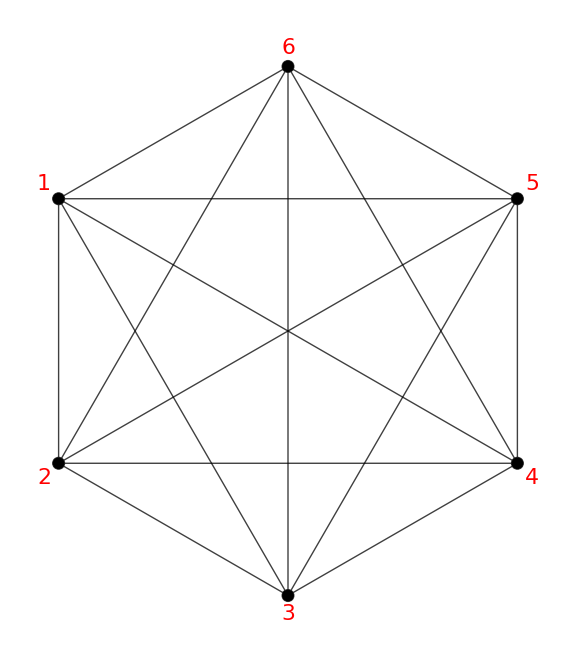

```mathematica
SeedRandom[36];

nNodes = 10;
nEdges = 18;
nNodes = 6;
nEdges = 13;
(*nNodes =6;
nEdges = 16;*)

(*g = CreateRandomGraph[nNodes,nEdges];*)

g = CreateFullGraph[nNodes];
nEdges = Length[EdgeList[g]]

(*Extract information from the input graph*)
nNodes=VertexCount[g];
nEdges=EdgeCount[g];
adjMat=AdjacencyMatrix[g];
edges=EdgeList[g];

vCoords = {{-1,-1},{-1,1},{1,1},{1,-1}};
Graph[g,VertexLabels->"Name",VertexStyle->Black,EdgeStyle->Directive[Black,Thick,Opacity[0.75]],ImageSize->Large,VertexLabelStyle->Directive[Black,22,Red]]

(*{dPhidWij,WijMatSymbols}=DPhikDWijMatrix[g,nNodes,nEdges];*)
```

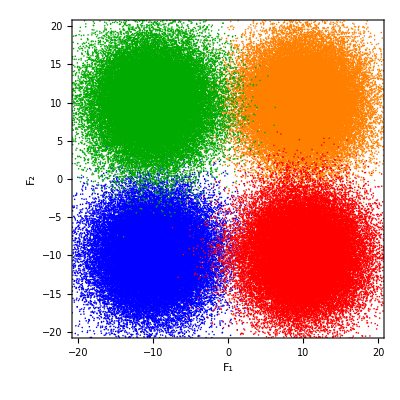

```mathematica
n=50000;  (*Sample size*)

fFac = 10;
off =0*{1,1};
μ1 =1*fFac*{-1,-1} +fFac*off;
(*μ2=1*fFac*{0.5,1}+fFac*off;*)
μ2=1*fFac*{1,1}+fFac*off;
μ3=1*fFac*{-1,1}+fFac*off;
μ4=1*fFac*{1,-1}+fFac*off;

(*μ1 =1*fFac*{1,1} +fFac*off;
μ2=1*fFac*{-1,1}+fFac*off;
μ3=1*fFac*{-1,-1}+fFac*off;
μ4=1*fFac*{1,-1}+fFac*off;*)

rho=0.0;  (*Correlation coefficient*)
sigma=fFac*0.4;

xy1 = RandomVariate[BinormalDistribution[μ1,{sigma,sigma},rho],n];
xy2 = RandomVariate[BinormalDistribution[μ2,{sigma,sigma},rho],n];
xy3 = RandomVariate[BinormalDistribution[μ3,{sigma,sigma},rho],n];
xy4 = RandomVariate[BinormalDistribution[μ4,{sigma,sigma},rho],n];
xyList = {xy1,xy2,xy3,xy4};
(*labels = {{1,-1,-1},{-1,1,-1},{-1,-1,1}};*)

Show[
ListPlot[xy1,PlotStyle->Blue,PlotRange->fFac*{{-2,2},{-2,2}}, FrameLabel->{"F_1","F_2"},AspectRatio->1],
ListPlot[xy2,PlotStyle->Orange],
ListPlot[xy3,PlotStyle->Darker@Green],
ListPlot[xy4,PlotStyle->Red]]
```

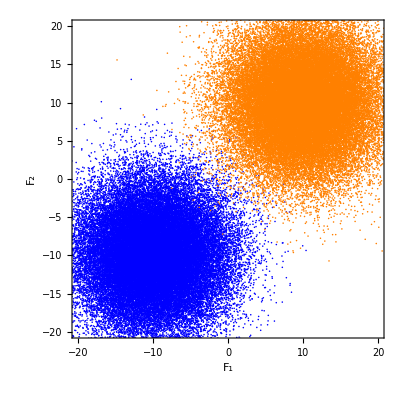

```mathematica
n=50000;  (*Sample size*)

fFac = 10;
off =0*{1,1};
μ1 =1*fFac*{-1,-1} +fFac*off;
μ2=1*fFac*{1,1}+fFac*off;

rho=0.0;  (*Correlation coefficient*)
sigma=fFac*0.5;

xy1 = RandomVariate[BinormalDistribution[μ1,{sigma,sigma},rho],n];
xy2 = RandomVariate[BinormalDistribution[μ2,{sigma,sigma},rho],n];
xyList = {xy1,xy2};
(*labels = {{1,-1,-1},{-1,1,-1},{-1,-1,1}};*)
labels = {{1,0},{0,1}};

Show[
ListPlot[xy1,PlotStyle->Blue,PlotRange->fFac*{{-2,2},{-2,2}}, FrameLabel->{"F_1","F_2"},AspectRatio->1],
ListPlot[xy2,PlotStyle->Orange]]
```

```mathematica
(*RandomSeed[36];*)

nIter = 2000;
timeStride = 10; 

numOuts = {{6},{4},{3},{5}}; (* how many output nodes - for multiclass*)
(*inputInds={{7},{11}}; (* which input edges *)*)
inputInds={{5,14},{15,11}}; (* which input edges - for cirlce*)

(*numOuts = {{6},{4}}; (* how many output nodes - for multiclass*)
(*inputInds={{7},{11}}; (* which input edges *)*)
inputInds={{5,14},{15,11}}; (* which input edges - for cirlce*)*)

repBool=False;
BijBool=False;
fth=5000*10^-1;

signs=ConstantArray[1,{Length[inputInds[[1]]]}];
signs = {1,1};

deltaE=1;
deltaF=0.5;

EjList = ConstantArray[0,{nNodes}];
FijList = ConstantArray[0,{nEdges}];
BijList = ConstantArray[0,{nEdges}];
EjList[[Flatten[numOuts]]]=-0;

WijMat= UpdateWeightMatrix[g,edges,nEdges, nNodes,adjMat, EjList, BijList,FijList];

EjListInit = EjList;
BijListInit=BijList;
FijListInit=FijList;


outsLabels = GetOutsLabels[nNodes,numOuts];

meanLists = {};
stdLists = {};


Do[
nInd = RandomInteger[Length[numOuts]-1]+1;

inputs = xyList[[nInd]][[iter]];
WijMatPre=MapInputToWijMat[inputs,inputInds,signs,g,edges,nEdges,nNodes,adjMat,EjList, BijList, FijList,BijBool,repBool];
piVecPre=GetStationaryVector[WijMatPre];

outsDiffs = outsLabels[[nInd]];
{piVecNudged,fluxesNudged,frenesiesNudged}=nudgedStationaryVector[inputs,inputInds,signs,numOuts,deltaE*outsDiffs,g,edges,nEdges,nNodes,adjMat,EjList,BijList,FijList,BijBool,repBool];

pisDiffs = piVecNudged -piVecPre;
EjList -= deltaF*pisDiffs;

piPrime=ComputepiAndPiprime[inputs, inputInds,signs,g,edges,nEdges,nNodes,False,EjList,BijList,FijList,adjMat,0.001,BijBool,repBool];
fluxesDiffs =(piVecNudged / piVecPre).piPrime;
FijList += deltaF*fluxesDiffs;
FijList=Clip[FijList,{-fth,fth}];

piPrime=ComputepiAndPiprime[inputs, inputInds,signs,g,edges,nEdges,nNodes,True,EjList,BijList,FijList,adjMat,0.001,BijBool,repBool];
fluxesDiffs =(piVecNudged / piVecPre).piPrime;
BijList += deltaF*fluxesDiffs;

If[Mod[iter,timeStride]==0,
{newMeans, newStds}=TestPredictions[meanLists,stdLists,10,xyList,inputInds,signs,numOuts,g,edges,nEdges,nNodes,adjMat,EjList, BijList, FijList,BijBool,repBool];
AppendTo[meanLists,newMeans];
AppendTo[stdLists,newStds];
];

,{iter,1,nIter}];

Print["Done."]
```

Done.

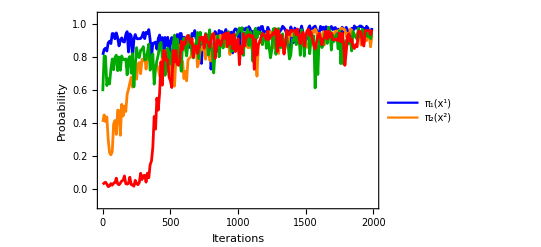

```mathematica
SetOptions[ListPlot,
Frame->True,
Axes->False,
FrameTicksStyle->Thickness[.001],
FrameStyle->Directive[Black,Thickness[0.004]],
LabelStyle->{FontFamily->"Arial",Black,FontSize->16}];

iters = Range[0,Length[meanLists]-1]*timeStride;
data1 = Transpose[{iters,meanLists[[;;,1]]}];
data2 = Transpose[{iters,meanLists[[;;,2]]}];
data3 = Transpose[{iters,meanLists[[;;,3]]}];
data4 = Transpose[{iters,meanLists[[;;,4]]}];

p=Legended[
Show[
ListPlot[data1,PlotRange->{{0,nIter},{-0.1,1.05}},PlotStyle->Blue,Joined->True,FrameLabel->{"Iterations","Probability"}],
ListPlot[data2,PlotStyle->Orange,PlotRange->Full,Joined->True],
ListPlot[data3,PlotStyle->Darker@Green,PlotRange->Full,Joined->True],
ListPlot[data4,PlotStyle->Red,PlotRange->Full,Joined->True]
],
Placed[
LineLegend[{Blue,Orange},{"π_1(x^1)", "π_2(x^2)"}
]
,{0.8,0.2}]
]
```

#### Memory patterns

```mathematica
trees = GetSpanningTrees[g,nNodes];
uiαArray=GetuiαArray[trees,edges,nEdges,nNodes];
viαArray=GetviαArray[trees,edges,inputInds, signs,nEdges,nNodes];
```

```mathematica
μvList = {};
Do[
Wij0=0;
μv=viαArray[[1,1]]*0;
ψs=0;
Do[
ψiα=Exp[uiαArray[[kk,nn]][[1]].EjList + uiαArray[[kk,nn]][[2]].BijList+uiαArray[[kk,nn]][[3]].FijList];
ψs=ψs+ψiα;
μv = μv + viαArray[[kk,nn]]*ψiα;
,{nn,1,Length[trees]}];

AppendTo[μvList,μv/ψs];
,{kk,1,nNodes}];
```

```mathematica
Nedges = {};
Do[
Nedgesij={};
Nedgesji={};
Do[
eij=edges[[e]][[1]]->edges[[e]][[2]];
eji=edges[[e]][[2]]->edges[[e]][[1]];
neij = 0;
neji =0;
Do[
oTree = OrientTree[trees[[nn]],kk];
If[MemberQ[oTree,eij],neij+=1];
If[MemberQ[oTree,eji],neji+=1];
,{nn,1,Length[trees]}];
AppendTo[Nedgesij,neij];
AppendTo[Nedgesji,neji];
,{e,1,nEdges}];
AppendTo[Nedges,{Nedgesij,Nedgesji}];
,{kk,1,nNodes}];
```

```mathematica
WijMat= UpdateWeightMatrix[g,edges,nEdges, nNodes,adjMat, EjList, BijList,FijList];
μeList = {};
Do[

μe={0,0};
norm = 0;
Do[

If[MemberQ[inputInds[[1]],e],
qija= 1/2;qjia=-1/2;,
qija=0;qjia=0;];

If[MemberQ[inputInds[[2]],e],
qijb= 1/2;qjib=-1/2;,
qijb=0;qjib=0;];

qij={qija,qijb};
qji={qjia,qjib};

Wij = WijMat[[edges[[e]][[1]],edges[[e]][[2]]]];
Wji = WijMat[[edges[[e]][[2]],edges[[e]][[1]]]];
Neij = Nedges[[kk]][[1]][[e]];
Neji = Nedges[[kk]][[2]][[e]];

μe += qij*Wij*Neij + qji*Wji*Neji;
norm += Wij*Neij + Wji*Neji;
,{e,1,nEdges}];

AppendTo[μeList,μe/norm];

,{kk,1,nNodes}];
```

```mathematica
kk=6;
μeList[[kk]]
μvList[[kk]]
```

{-0.315787,-0.00120289}

{-0.950938,-0.319948}

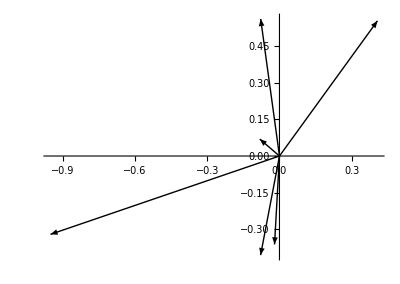

```mathematica
vectors={{1,2},{2,1},{1,-1},{-2,1}}; (*your list of 2D vectors*)

Show[
Graphics[Table[Arrow[{{0,0},v}],{v,μvList}],Axes->True,AxesOrigin->{0,0},PlotRange->All]
(*,
Graphics[Table[Arrow[{{0,0},v}],{v,μeList}],Axes->True,AxesOrigin->{0,0},PlotRange->All]*)
]
```

```mathematica
D[pp[x]Log[ppg[x]],x]//Simplify
```

Log[ppg[x]] pp'[x]+(pp[x] ppg'[x])/ppg[x]

#### MI density

```mathematica
piMarginal = ConstantArray[0,{nNodes}];
nSamples = 1000;
Do[
nInd = RandomInteger[Length[numOuts]-1]+1;
inputs = xyList[[nInd]][[iter]];
WijMatPre=MapInputToWijMat[inputs,inputInds,signs,g,edges,nEdges,nNodes,adjMat,EjList, BijList, FijList,BijBool,repBool];
piMarginal+=GetStationaryVector[WijMatPre];
,{iter,1,nSamples}];
piMarginal= piMarginal/nSamples;
```

{0.00105768,0.000578559,0.242065,0.243968,0.229487,0.282843}

```mathematica
trees = GetSpanningTrees[g,nNodes];
uiαArray=GetuiαArray[trees,edges,nEdges,nNodes];
viαArray=GetviαArray[trees,edges,inputInds, signs,nEdges,nNodes];
piF[x_,y_]:=Evaluate[GetpiVecTrees[nNodes,trees,EjList,BijList,FijList,{xx,yy},uiαArray,viαArray]/.{xx->x,yy->y}];
```

```mathematica
piF[0,0]
```

{0.00226974,0.00068219,0.22175,0.136775,0.529443,0.109079}

```mathematica
MIDensity[x_,y_]:=Total[piF[x,y]Log[piF[x,y]/piMarginal]]
Ent[x_,y_]:=-Total[piF[x,y]Log[piF[x,y]]]
```

```mathematica
Plot3D[Ent[x,y],{x,-mf,mf},{y,-mf,mf},PlotPoints->30]
```

-Graphics3D-

```mathematica
mf = 40;
Plot3D[{MIDensity[x,y],Ent[x,y]},{x,-mf,mf},{y,-mf,mf},PlotPoints->30]
```

-Graphics3D-

```mathematica
ks = 1;
FindMaximum[MIDensity[x,y]-ks/2 (Sqrt[x^2+y^2]-10)^2,{{x,10},{y,-10}}]
```

{1.41096,{x→4.87197,y→-8.73484}}

```mathematica
mf= 20;
ks = 0.01
Plot3D[{MIDensity[x,y]-ks/2 (Sqrt[x^2+y^2]-10)^2},{x,-mf,mf},{y,-mf,mf},PlotPoints->30]
```

0.01

-Graphics3D-

0.01

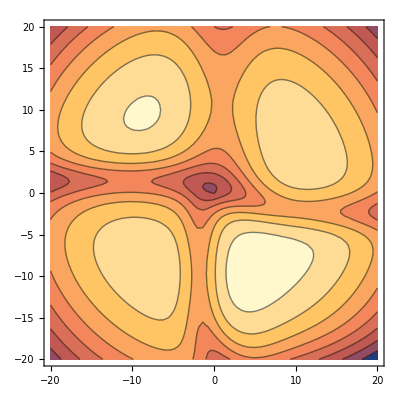

```mathematica
ks = 0.01
Show[
ContourPlot[{MIDensity[x,y]-ks/2 (Sqrt[x^2+y^2]-10)^2},{x,-mf,mf},{y,-mf,mf},PlotPoints->30](*,
ListPlot[xy1,PlotStyle->Blue,PlotRange->fFac*{{-2,2},{-2,2}}, FrameLabel->{"F_1","F_2"},AspectRatio->1],
ListPlot[xy2,PlotStyle->Orange],
ListPlot[xy3,PlotStyle->Darker@Green],
ListPlot[xy4,PlotStyle->Red]*)]
```